# Tarea 1

## Carlos Salinas González

## Ejercicio 3, inciso a)

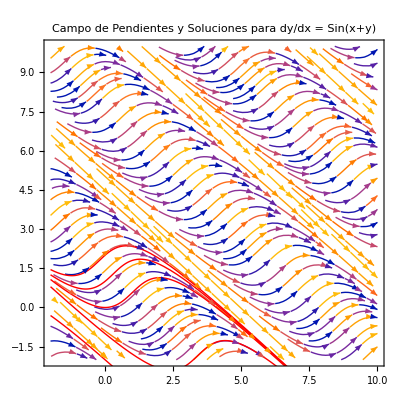

```mathematica
fieldA = StreamPlot[{1, Sin[x + y]}, {x, -2, 10}, {y, -2, 10}, 
  StreamStyle -> Gray, StreamPoints -> Fine];


solutionsA = Table[
   NDSolve[{y'[x] == Sin[x + y[x]], y[0] == y0}, y, {x, -2, 10}], 
   {y0, -2, 2, 1}];

solutionCurvesA = 
  Table[Plot[Evaluate[y[x] /. solutionsA[[i]]], {x, -2, 10}, 
    PlotStyle -> {Thick, Red}], {i, Length[solutionsA]}];


Show[fieldA, solutionCurvesA, 
 PlotLabel -> "Campo de Pendientes y Soluciones para dy/dx = Sin(x+y)"]
```

## Ejercicio 3, inciso b)

NDSolve::ndsz: At x == 0.215973, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 0.404719, step size is effectively zero; singularity or stiff system suspected.

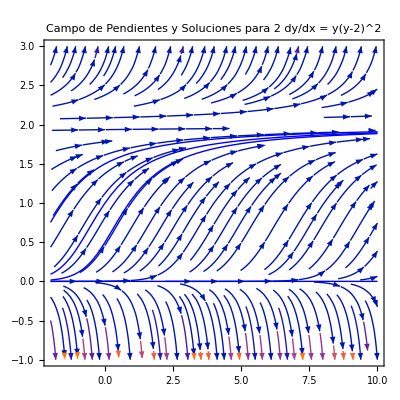

```mathematica
fieldB = StreamPlot[{1, (y (y - 2)^2)/2}, {x, -2, 10}, {y, -1, 3}, 
  StreamStyle -> Gray, StreamPoints -> Fine];


solutionsB = Table[
   NDSolve[{y'[x] == (y[x] (y[x] - 2)^2)/2, y[0] == y0}, y, {x, -2, 10}, 
    Method -> "StiffnessSwitching"], 
   {y0, -1, 1.8, 0.5}];  

solutionCurvesB = 
  Table[Plot[Evaluate[y[x] /. solutionsB[[i]]], {x, -2, 10}, 
    PlotStyle -> {Thick, Blue}], {i, Length[solutionsB]}];


Show[fieldB, solutionCurvesB, 
 PlotLabel -> "Campo de Pendientes y Soluciones para 2 dy/dx = y(y-2)^2"]
```

## Ejercicio 6

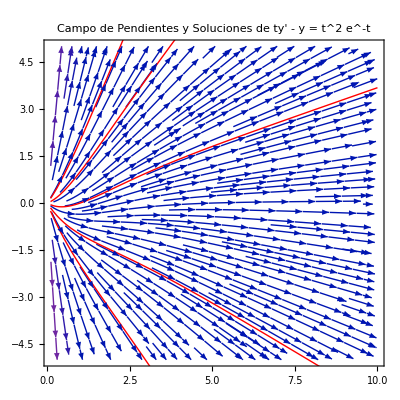

```mathematica
eq[t_, y_] := (y + t^2 Exp[-t])/t


field = StreamPlot[{1, eq[t, y]}, {t, 0.1, 10}, {y, -5, 5}, 
   StreamStyle -> Gray, StreamPoints -> Fine];


solutions = Table[
   NDSolve[{y'[t] == eq[t, y[t]], y[1] == y0}, y, {t, 0.1, 10}], 
   {y0, -2, 2, 1}];

solutionCurves = Table[
   Plot[Evaluate[y[t] /. solutions[[i]]], {t, 0.1, 10}, 
    PlotStyle -> {Thick, Red}], {i, Length[solutions]}];


Show[field, solutionCurves, 
 PlotLabel -> "Campo de Pendientes y Soluciones de ty' - y = t^2 e^-t"]
```